Math 456
Lab #2 by Julius Duthoy
Cobweb Function

```mathematica
cobweb[f_,xmin_,xmax_,n_,start_]:=
Show[{Plot[{x,f[x]},{x,xmin,xmax}],ListPlot[{Partition[Riffle[NestList[f,start,n],NestList[f ,start,n]],2,1]},Joined->True, PlotStyle->Dashed]}, AspectRatio->Automatic]
```

1. x -> x (1 - x) on {0 <= x <= 1}

```mathematica
cobweb[# (1 - #) &, 0, 1, 5, 0.5]
```

```mathematica
cobweb[# (1 - #) &, 0, 1, 5, 0.8]
```

```mathematica
cobweb[# (1 - #) &, 0, 1, 5, 1.0]
```

```mathematica
cobweb[# (1 - #) &, 0, 0.1, 5, 0.05]
```

Attracting Fixed Points: x=0
Characteristics:
Cobweb diagram iterates towards the fixed point. 
There are no trajectories on [0,1] that are not attracted to x=0. 
Starting points
- x=0.5 was chosen since it is at the local maximum where f’(x)=0. Nevertheless, the cobweb diagram indicates that the point x=0.5 maps closer to x=0 with every iterate. 
- x=0.8 was chosen as a representative point where f’(x)<0 on the interval [0,1]. The cobweb indicates that this point too moves closer to x=0 with every iterate. We notice that points closer to x=1 on [0.5,1] in fact map closer to x=0 in a single iterate. 
- x=1 was chosen since its image is 0 which is also the fixed point, that is f(1)=0=f(0).  
- x=0.05 was chosen to clearly see if the map lies above or below the line y=x closer to the fixed point f(0)=0. We see that it ineed lies above y=x, and that the cobweb does show that the point x=0.05 iterates toward x=0. 
Repelling Fixed Points: None
Conjectures on Global Dynamics
There exist only one fixed point at x=0. The basin of attraction is the closed interval [0,1]. Points on (-inf, 0) are repelled off/attracted to -inf. Points on (1,inf) are mapped to the interval (-inf, 0) in one iteration, and are also repelled off to -inf.

2. x->2x(1-x) on {0<=x<=1}

```mathematica
cobweb[2# (1 - #) &, 0, 1, 5, 0.2]
```

```mathematica
cobweb[2# (1 - #) &, 0, 1, 5, 0.5]
```

```mathematica
cobweb[2# (1 - #) &, 0, 1, 5, 0.7]
```

```mathematica
cobweb[2# (1 - #) &, 0, 1, 5, 1]
```

Attracting Fixed Points: x=0.5
Characteristics:
Cobweb diagram iterates towards the fixed point. 
The only trajectories not attracted to the fixed point x=0.5 is the fixed point x=0 and the point x=1. However, the image of x=1 is f(1)=0=f(0). In other words, x=1 maps directly to the fixed point x=0.  
Starting points
- x=0.2 was chosen as a representative point where x=0.2<0.5 and f(0.2)<f(0.5) with f(x) increasing, or f’(x)>0 on (0,0.5). The cobweb indicates that this point moves closer to x=0.5 with every iterate. 
- x=0.5 was chosen since it is the attracting fixed point itself. We may note that f’(0.5)=0 as well. As expected, there is no cobweb since it is fixed and each map simply stays at the point (0.5,0.5).   
- x=0.7 was chosen as a representative point where x=0.7>0.5 and f(0.7)>f(0.5) with f(x) decreasing, or f’(x)<0 on (0.5,0). The cobweb indicates that this point maps to the interval (0.0.5) in one iterate. It then is mapped closer to the attracting fixed point x=0.5 with every iterate.   
- x=1 was chosen since it’s image is the same as that of the fixed point x=0. In other words f(1)=f(0)=0. As expected the cobweb indicates that x=1 maps directly to the fixed point x=0. 
Repelling Fixed Points: x=0
Each starting point repelled away from x=0 except for x=1, which had the same image as x=0. 
Conjectures on Global Dynamics
There exist 2 fixed points on the interval [0,1]. The basin of attraction for the point x=0.5 is the open interval (0,1). Points on (-inf, 0) are repelled off/attracted to -inf. Points on (1,inf) are mapped to the interval (-inf, 0) in one iteration, and are also repelled off to -inf.  The only points mapped onto the repelling fixed point x=0 are x=0 itself and x=1.

#### 3. x-> 4x(1-x) on {0<=x<=1}

```mathematica
cobweb[4# (1 - #) &, 0, 1, 13, 0.1]
```

```mathematica
cobweb[4# (1 - #) &, 0, 1, 5, 0.15]
```

#### Interval (0, 0.15) L->L On this interval the first iterate is mapped back onto (0, 0.5), the left side of the interval. Clearly the end point (not included in the interval) x=0 is fixed and does not move from this point when iterated. The end point x=0.15 maps to the maximum point x=0.5 which maps to x=1. In turn, the point x=1 maps back to the end point x=0. In other words f(0.15)=0.5, f(0.5)=0, and f(0)=0 fixed. Note that f’(0.5)=0.

```mathematica
cobweb[4# (1 - #) &, 0, 1, 5, 0.25]
```

```mathematica
cobweb[4# (1 - #) &, 0, 1, 5, 0.3]
```

#### Interval (0.15, 0.5) L->R On this interval points are mapped from the left to the right side (0.5, 1). We may note that x=0.25 (not part of the interval) directly maps to the fixed point x=0.75.

```mathematica
cobweb[4# (1 - #) &, 0, 1, 5, 0.75]
```

```mathematica
cobweb[4# (1 - #) &, 0, 1, 13,0.8]
```

```mathematica
cobweb[4# (1 - #) &, 0, 1, 5, 0.7]
```

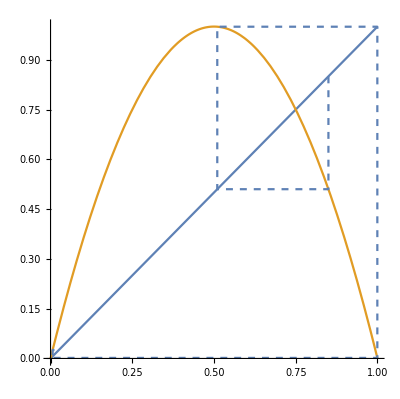

```mathematica
cobweb[4# (1 - #) &, 0, 1, 5, 0.85]
```

#### Interval (0.5, 0.85) R->R On this interval points are mapped back onto the right side (0.5, 1). However, we also note that the point x=0.75 is fixed and, thus, continually maps back to itself on this interval. We may also note that the endpoint x=0.5, which is not included, maps to x=0 in 2 iterates as we stated earlier. The other endpoint, x=0.85 maps to 0.5 which, as we just mentioned, will map to x=0.

```mathematica
cobweb[4# (1 - #) &, 0, 1, 5, 0.9]
```

#### Interval (0.85, 1) R->L On this interval points are mapped onto the left side (0, 0.5) in one iteration. Of course, as we have stated, x=1 maps directly to x=0. Global Dynamics If we drew the transition graph for the map we would find that it is fully connected, meaning all possible sequences of L and R are possible. This implies that the map has periodic solutions of every period. However, from trying various starting points some eventually map to the fixed point x=0 and some map to the fixed point x=0.75. Yet, neither are attracting. Still, any starting point on [0,1] stays on [0,1]. Therefore, the interval itself is fixed in a way (it is a self map). Outside of the interval (0,1), Points on (-inf, 0) are repelled off/attracted to -inf. Points on (1,inf) are mapped to the interval (-inf, 0) in one iteration, and are also repelled off to -inf.

## 4. x->2.9x(1-x) on {0<=x<=1}

```mathematica
cobweb[2.9# (1 - #) &, 0, 1, 10, 0.22]
```

Interval (0, 0.22) L→L
On this interval the points are mapped back onto the left side (0, 0.5). However,these points are eventually mapped closer and closer to the point x=0.655, the fixed point. The end point x=0.22 which maps to x=0.5, also iterates closer to the fixed point x=0.655.

### Interval(0.22,0.5) L→R On this interval the points are mapped from the left side to the right interval (0.5,0.77), which moves closer to the fixed point x=0.655.

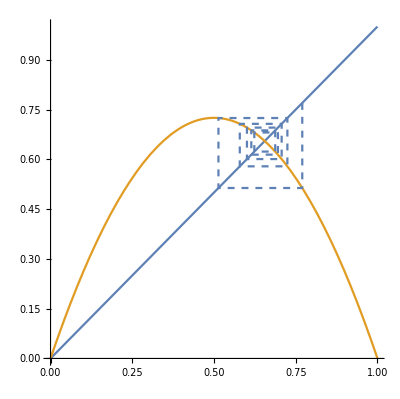

```mathematica
cobweb[2.9# (1 - #) &, 0, 1, 10, 0.77]
```

#### Interval (0.5,0.77) R->R On this interval points are mapped from (0.5, 0.77) back onto (0.5, 0.77), moving closer to the fixed point x=0.655, as stated in the previous interval.

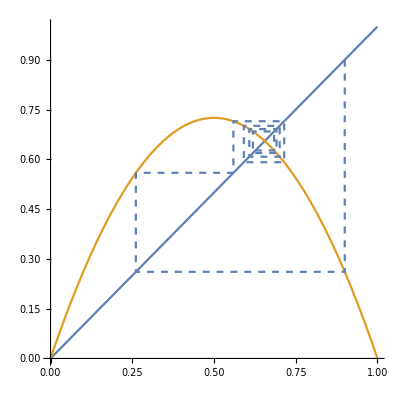

```mathematica
cobweb[2.9# (1 - #) &, 0, 1, 10, 0.9]
```

### Interval (0.77,1) R->L On this interval points are mapped from the right side to the left side. It is important to note that the points are eventually mapped onto the interval (0.5, 0.77), which we know iterates closer to the fixed point x=0.655. Global Dynamics Attracting Fixed Point: x=0.655 Repelling Fixed Point: x=0 Characteristics: In general, points can map from the left to right and vice versa. However, as soon as a point is mapped onto the closed interval [0.5,0.77] they will stay on that interval and iterate toward x=0.655.

5. x→3x(1-x) on{0<=x<=1}

cobweb[3# (1 - #) &, 0, 1, 10, 0.21]

### Interval (0,0.21) L→L On the interval the points are mapped back to the left side. However, they are eventually mapped to the interval (0.5, 0.78) which seems to slowly iterate towards the fixed point x=2/3. I have used the word "seems" due to the fact that I have iterated the map 1000 times and it only moves a small distances closer to the fixed point. It is important to note that a point on this interval may map to x=0.21 which maps directly to the fixed point x= 2/3.

### Interval (0.21,0.5) L→R Points on this interval map to the interval (0.5, 0.78) which seems to iterate closer to the fixed point x= 2/3 as stated above.

```mathematica
cobweb[3# (1 - #) &, 0, 1, 10, 0.78]
```

### Interval (0.5,0.78) R->R Points on this interval self-map back to itself (0.5,0.78) but still iterate toward the fixed point x= 0.6667. We may note that this interval will give the itinerary {RRRRR...}, which is similar to a fixed point.

```mathematica
cobweb[3# (1 - #) &, 0, 1, 10, 0.9]
```

### Interval (0.78, 1) R->L On this interval points are mapped back to the left side of the interval. They then follow the patterns discussed above on the intervals (0,0.21) and (0.21, 0.5). Both of these intervals then map to the fixed point x= 0.6667.

6. x→3.1x(1-x) on{0<=x<=1}

```mathematica
cobweb[3.1# (1 - #) &, 0.5, 0.9, 50, 0.2]
```

### Interval (0,0.2) L->L On this interval points are mapped from the left hand side back to the left hand side of the map. However, it seems as if they are eventually mapped to the interval (0.5,0.8), which we will look at later.

```mathematica
cobweb[3.1# (1 - #) &, 0.5, 0.9, 50, 0.325]
```

### Interval (0.2,0.5) L->R On this interval points are mapped from the left directly to the right side of the interval. Once again points seem to settle down on the interval (0.5,0.8). Yet, if we choose a point that maps close enough to the fixed point, say x=0.325, we see that the oscillations grow back out!

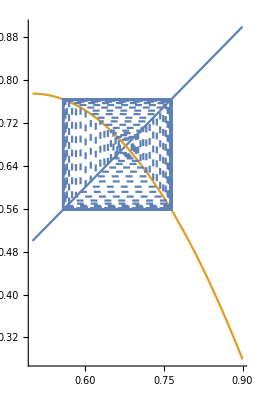

```mathematica
cobweb[3.1# (1 - #) &, 0.5, 0.9, 50, 0.6666]
```

```mathematica
cobweb[3.1# (1 - #) &, 0.5, 0.9, 50, 0.8]
```

### Interval (0.5,0.8) This interval seems to be an attracting interval. We are left with the possibility that the oscillations decrease if we can iterate long enough. However, if we choose a point close enough to the fixed point, say x=0.6666, since our actual fixed point is x=2/3, we see that the oscillations increase back out.

```mathematica
cobweb[3.1# (1 - #) &, 0.55, 0.9, 5, 0.9]
```

### Interval (0.8,1) R->L On the final interval of the map points are mapped from the right side to the left side. However, once again they are mapped onto the interval (0.5,0.8). Yet, we can see that the iterates will oscillate out from only 5 iterations. Global Dynamics No matter where the iterations start, they are eventually mapped onto the interval (0.5,0.8). Once on this interval they are eventually mapped back out again. Most interestingly, the closer they are mapped to the fixed point x=2/3 they faster the iterations map back out.